## Assignment 3

4.4.7

(7) A hemispherical chunk of fat has radius a=2 cm. The flat side of the hemisphere sits on a stove, at height z=0.  At t=0 the temperature of the fat is T_o=300 K. At this time, the stove is turned on and the surface at z=0 heats according to T=T_o+(T_1-T_o)tanh(t/60), where T_1=400 K, and times are in seconds. Assuming that the rest of the fat surface exposed to air has an insulating boundary condition, and that the fat has the thermal properties of water, find T(r,θ,t). Plot the temperature vs. time at the point farthest from the stove.

### Solution

The solution is in terms of spherical eigenmodes of the Laplacian operator ψ_(l  n)(r,θ)(only cylindrically symmetric modes need be kept): T = u(r,θ,t) + ΔT(r,θ,t). Boundary conditions imply that we want a function u(r,θ,t) that equals T_o+(T_1-T_o)tanh(t/60) at θ = π/2 and has ∂u/∂r|_(r=a)=0.  The simplest choice is just u =T_o+(T_1-T_o)tanh(t/60) .

```mathematica
Clear["Global`*"]
```

```mathematica
u[t_] = T0 + (T1 - T0) Tanh[t/60];
```

Then the rest of the solution satisfies the heat equation with a source given by

```mathematica
Sb[t_] = -D[u[t],t]
```

-1/60 (-T0+T1) Sech[t/60]^2

We then write ΔT(r,θ,t) in terms of spherical eigenmodes of the Laplacian operator

```mathematica
Clear[ψ]
```

```mathematica
ψ[k_,l_,r_,θ_] = LegendreP[l,Cos[θ]] BesselJ[l+1/2,k r/a]/Sqrt[r];
```

The values of k needed to match boundary conditions will be determined shortly. In order to satisfy the boundary condition at θ=Pi/2 that the eigenmodes vanish, we require l=oddintegers.

Also, note that we will have need of the following inner product (ψ_(l n), 1)/(ψ_(l n),ψ_(l n))later. It is useful to do this inner product analytically. The latest version of Mathematica has some trouble with this, but can be coaxed to giving results. For the numerator,

```mathematica
num=Integrate[Integrate[ψ[k,l,r,θ] r^2 Sin[θ],{θ,0,Pi/2}],{r,0,a},Assumptions->a>0&&k>0&&l≥ 0]
```

(2^(-5/2-l) a^(5/2) k^(1/2+l) √π HypergeometricPFQRegularized[{(3+l)/2},{(5+l)/2,3/2+l},-k^2/4])/Gamma[1-l/2]

For the denominator, I use the known result (which Mathematica has somewehow forgotten), ∫_0^(π/2) [P_l(cosθ)]^2 sinθⅆθ=1/(2l+1).

For instance,

```mathematica
Integrate[LegendreP[5,x]^2,{x,0,1}]
```

1/11

```mathematica
denom=Integrate[1/(2l+1)  BesselJ[l+1/2,k r/a]^2 r,{r,0,a},Assumptions->a>0&&k>0&&l≥ 0]
```

(a^2 k^(1+2 l) Gamma[1+l] HypergeometricPFQRegularized[{1+l},{5/2+l,2+2 l},-k^2])/((2+4 l) √π)

```mathematica
c[l_,k_]= num/denom;
```

There is no way to solve for the eigenvalues k except by brute force using findroot, for each value of l:

```mathematica
list=Simplify[D[Table[BesselJ[l+1/2,k r/a]/Sqrt[r],{l,0,11}],r]/.r->a];
```

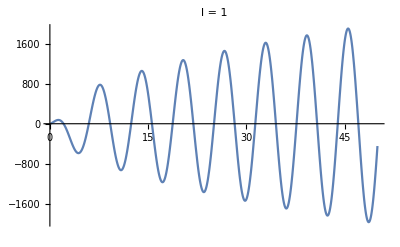
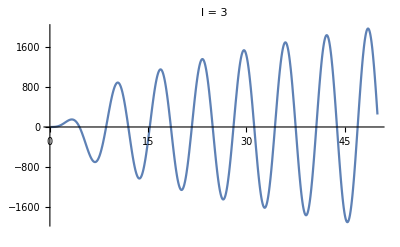
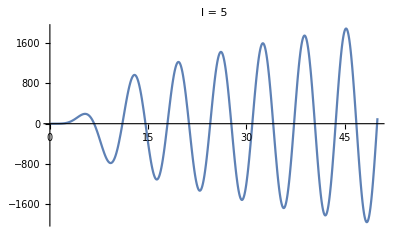
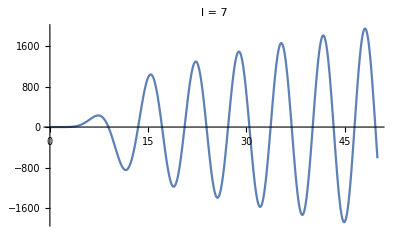
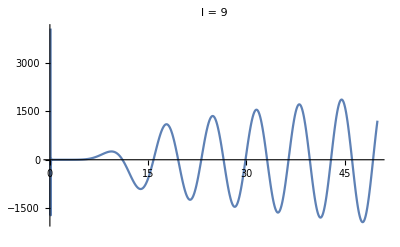
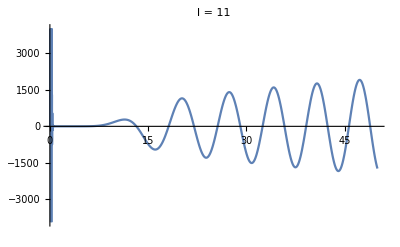

```mathematica
pl=Table[Plot[list[[l+1]]/.a->0.02,{k,.1,50},PlotLabel->"l = "<>ToString[l]],{l,1,11,2}]
```

Roots obviously increase as l increases.

By examining these graphs, after some trial and error I decide that roots are roughly at
r=1.9+1.2(l-1)+(n-1)(Pi+2n/(1+1.1n^2/(1+.15 (l-1))))

```mathematica
rguess[n_,l_]:= 1.9+1.2(l-1)+(n-1)(Pi+2n/(1+1.1n^2/(1+.15 (l-1))));
```

```mathematica
Table[ListPlot[Table[{ rguess[n,l],0},{n,1,12}],PlotStyle->{Red,PointSize[0.02]}],{l,1,11,2}];
```

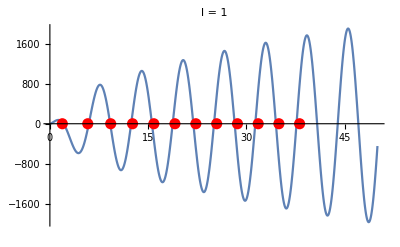
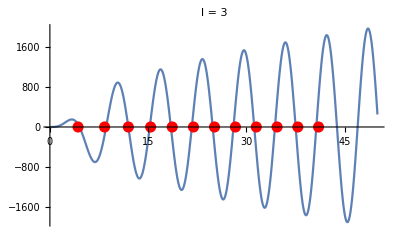
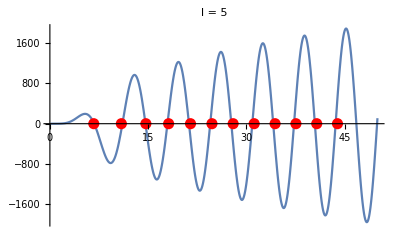
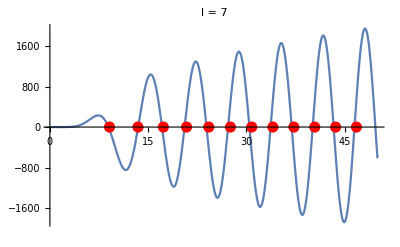
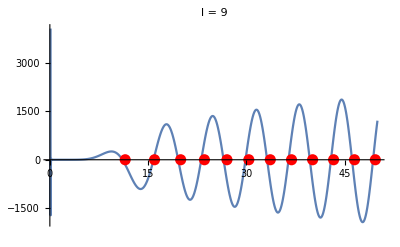
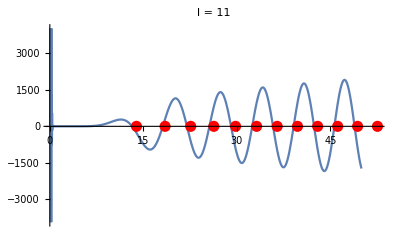

```mathematica
Table[Show[pl[[n]],%[[n]],PlotRange->All],{n,1,Length[pl]}]
```

```mathematica
a=0.02
```

0.02

```mathematica
Clear[k]
```

```mathematica
k[l_,n_] := (k[l,n] = k/.FindRoot[Evaluate[list[[l+1]]==0],{k,rguess[n,l] }])/; l∈Integers&&n∈Integers
```

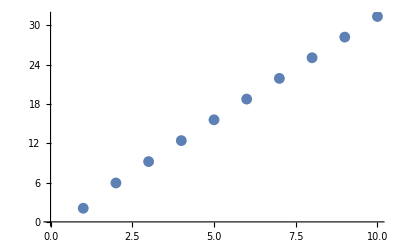
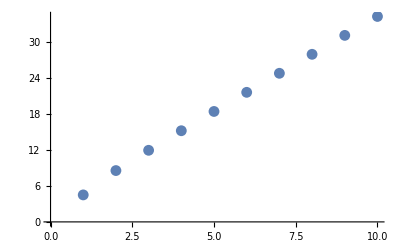
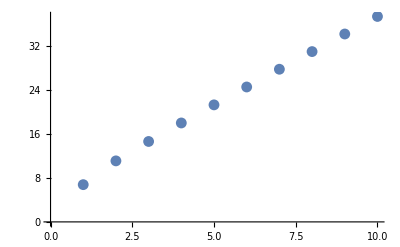
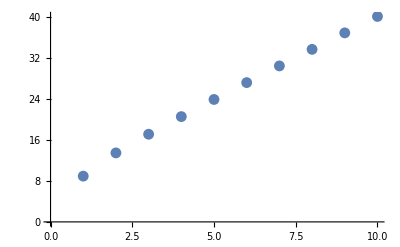
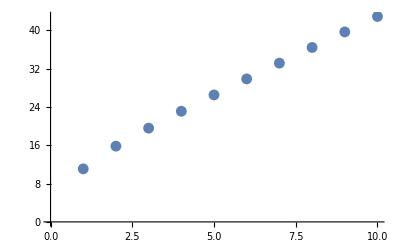
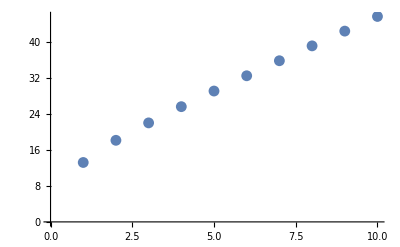

```mathematica
Table[ListPlot[Table[k[l,n],{n,1,10}],PlotRange->All],{l,1,11,2}]
```

Here's the view of a couple of the eigenmodes. As expected at r=a they have zero slope:

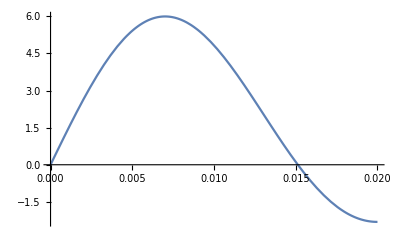

```mathematica
Plot[ψ[k[1,2],1,r,0],{r,0,a}]
```

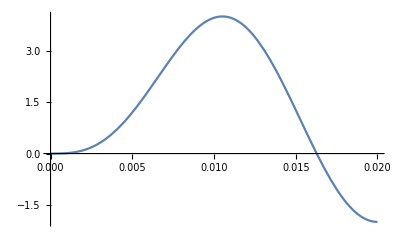

```mathematica
Plot[ψ[k[3,2],3,r,0],{r,0,a}]
```

Thus, ΔT(r,θ,t)= ∑_(l n) A_(l n)(t) ψ_(l n)(r,θ), where the A_(l n)'s satisfy the following ODE:
A'(t) = -χ (k_(l n))^2 A(t)/a^2 + S(t) (ψ_(l n), 1)/(ψ_(l n),ψ_(l n)) .

I solve the ODE numerically ( but one can also solve it analytically). Note we require the inner product  (ψ_(l n), 1)/(ψ_(l n),ψ_(l n)).
I work out analytic forms for the inner product for each l value but one can do this numerically as well, provided the numerics is accurate. There is a general form for c in terms of hypergeometric functions given above , but the latest version of Mathematica dhas a hard time finding it. Another way to go is by doeing the integrals for each separate value of l. This takes a little longer.

```mathematica
Clear[a,c1]
```

```mathematica
Do[Print[c1[l,k_]=Integrate[1 ψ[k,l,r,θ] r^2 Sin[θ],{r,0,a},{θ,0,Pi/2}]/Integrate[ψ[k,l,r,θ]^2 r^2 Sin[θ],{r,0,a},{θ,0,Pi/2}]],{l,1,11,2}]
```

(3 √a √k √(2 π) (1+(√a √(k/a))/(√k)-2 Cos[k]-k Sin[k]))/(2 (-1+k^2+Cos[2 k])+k Sin[2 k])

-(7 √a k^(7/2) √(π/2) (8 k+7 k Cos[k]+(-15+k^2) Sin[k]))/(4 (-45-15 k^2-6 k^4+k^6+(45-75 k^2+6 k^4) Cos[2 k]+k (180-60 k^2+k^4) Cos[k] Sin[k]))

(11 k^6 √(π/2) ((16 k^5)/(k/a)^(5/2)-(a^(5/2) (k (-315+16 k^2) Cos[k]+(315-105 k^2+k^4) Sin[k]))/(√k)))/(8 a^2 (-99225-14175 k^2-1260 k^4-105 k^6-15 k^8+k^10+15 (6615-12285 k^2+2604 k^4-119 k^6+k^8) Cos[2 k]+k (396900-207900 k^2+20160 k^4-420 k^6+k^8) Cos[k] Sin[k]))

-((75 k^8 √(π/2) ((128 k^7)/(5 (k/a)^(5/2))+(a^(5/2) (k (27027-2772 k^2+29 k^4) Cos[k]+(-27027+11781 k^2-378 k^4+k^6) Sin[k]))/(√k)))/(64 a^2 (-1404728325-127702575 k^2-6548850 k^4-259875 k^6-9450 k^8-378 k^10-28 k^12+k^14+7 (200675475-383107725 k^2+98232750 k^4-7509645 k^6+203310 k^8-1854 k^10+4 k^12) Cos[2 k]+k (5618913300-3235131900 k^2+434843640 k^4-19667340 k^6+315000 k^8-1512 k^10+k^12) Cos[k] Sin[k])))

(133 k^10 √(π/2) ((256 k^9)/(7 (k/a)^(5/2))-(a^(5/2) (k (-4922775+617760 k^2-12870 k^4+46 k^6) Cos[k]+(4922775-2258685 k^2+109395 k^4-990 k^6+k^8) Sin[k]))/(√k)))/(128 a^2 (-69850115960625-4656674397375 k^2-168567399000 k^4-4469590125 k^6-99324225 k^8-2027025 k^10-41580 k^12-990 k^14-45 k^16+k^18+45 (1552224799125-3000967944975 k^2+831599168400 k^4-76380329025 k^6+2957879925 k^8-52117065 k^10+409332 k^12-1254 k^14+k^16) Cos[2 k]+k^17 Cos[k] Sin[k]+139700231921250 k Sin[2 k]-83820139152750 k^3 Sin[2 k]+12754933191000 k^5 Sin[2 k]-748008711450 k^7 Sin[2 k]+19479710250 k^9 Sin[2 k]-231080850 k^11 Sin[2 k]+1164240 k^13 Sin[2 k]-1980 k^15 Sin[2 k]))

-((23 √a k^(23/2) √(π/2) (1024 √a k^(17/2) √(k/a)+21 k (1527701175-207850500 k^2+5797935 k^4-42900 k^6+67 k^8) Cos[k]+21 (-1527701175+717084225 k^2-41132520 k^4+589875 k^6-2145 k^8+k^10) Sin[k]))/(512 (-9002073394657468125-473793336560919375 k^2-13271522032518750 k^4-265430440650375 k^6-4298468674500 k^8-60786425700 k^10-794593800 k^12-10135125 k^14-135135 k^16-2145 k^18-66 k^20+k^22+33 (272790102868408125-531222831901636875 k^2+153547488242898750 k^4-15472717909023375 k^6+707944765027500 k^8-16464525304500 k^10+202854342600 k^12-1311362325 k^14+4164615 k^16-5525 k^18+2 k^20) Cos[2 k]+k^9 (7724507410620000-5368102740 k^6-8580 k^10+k^12) Cos[k] Sin[k]+18004146789314936250 k Sin[2 k]-11055177853088118750 k^3 Sin[2 k]+1795371500559136500 k^5 Sin[2 k]-119443698292668750 k^7 Sin[2 k]-65258156363400 k^11 Sin[2 k]+584918334000 k^13 Sin[2 k]+5675670 k^17 Sin[2 k])))

```mathematica
a=1/50;
```

or numerically:

```mathematica
Clear[cn]
```

```mathematica
cn[l_,n_] :=cn[l,n]=NIntegrate[1 ψ[SetPrecision[k[l,n],20],l,r,θ] r^2 Sin[θ],{r,0,a},{θ,0,Pi/2},WorkingPrecision->20]/NIntegrate[ψ[SetPrecision[k[l,n],20],l,r,θ]^2 r^2 Sin[θ],{r,0,a},{θ,0,Pi/2},WorkingPrecision->20]
```

But note that these numerical integrals must be done at high precision to work, and take quite a while to evaluate.

```mathematica
cn[3,2]//Timing
```

{42.25568,-0.1160836926513640289}

```mathematica
c[3,k[3,2]]//Timing
```

{0.00143,-0.116084}

```mathematica
c1[3,k[3,2]]//Timing
```

{0.0001,-0.116084}

```mathematica
χ = .59/4.19*^6
```

1.40811×10^-7

```mathematica
T1 = 400;T0=300;a=0.02;
```

```mathematica
Clear[A]
```

```mathematica
A[l_,n_]:= A[l,n] = A/.NDSolve[{A'[t] == -χ k[l,n]^2 A[t]/a^2 + c[l,k[l,n]]Sb[t] ,A[0]==0},A,{t,0,2000}][[1]]
```

```mathematica
A[11,1]
```

InterpolatingFunction[{{0., 2000.}}, <>]

```mathematica
ΔT[r_,θ_,t_] = Sum[A[l,n][t] ψ[k[l,n],l,r,θ],{l,1,11,2},{n,1,9}];
```

```mathematica
T[r_,θ_,t_] = u[t] + ΔT[r,θ,t];
```

```mathematica
T[.1,.2,200]
```

381.93

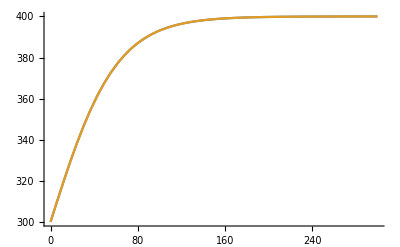

```mathematica
Plot[{u[t],T[a/2,Pi/2,t]},{t,0,300},PlotRange->All]
```

:The boundary condition on the bottom of the hemisphere is being matched. Note that the bottom reaches its final temperautre in about 200 seconds.

At the very top of the glob, where the temperature is lowest:

The initial fluctuation is numerical error due to the rather small number of modes kept.  In actuality we expect the top of the fat glob to remain at  constant temperature, 300 K,  until it begins to heat, apparently at around 100 sec. The solution becomes better as time progresses. But this is taking a very long time to heat up!

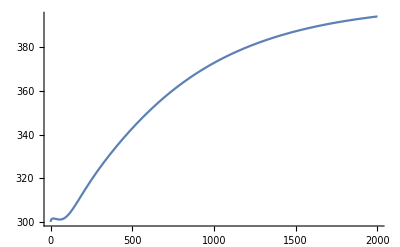

```mathematica
Plot[T[a/2,0,t],{t,0,2000},PlotRange->All]
```

Just  for fun, I will plot the temperature versus time as a series of contour plots, for 0<t<1000 sec.

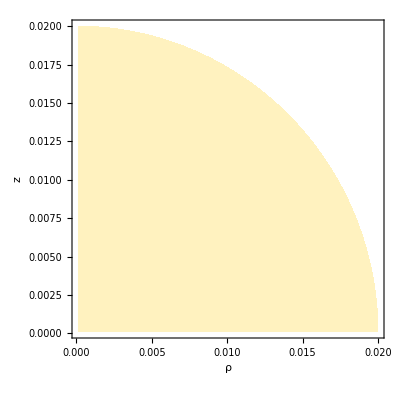
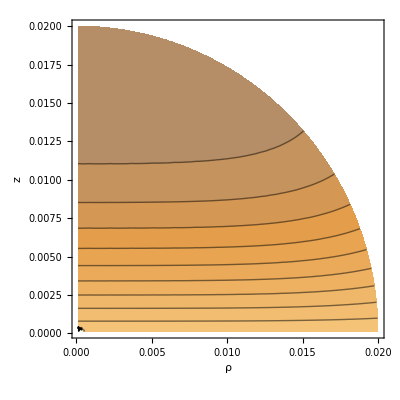
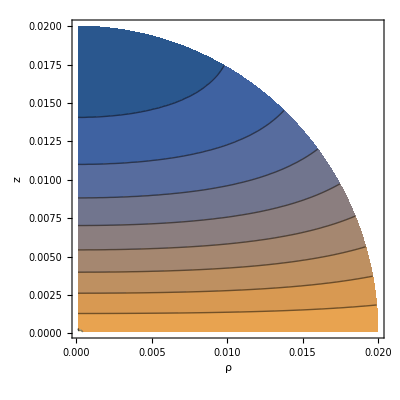
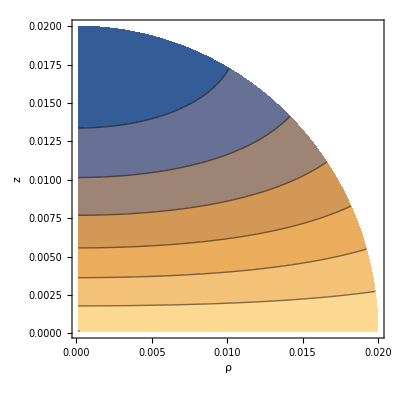
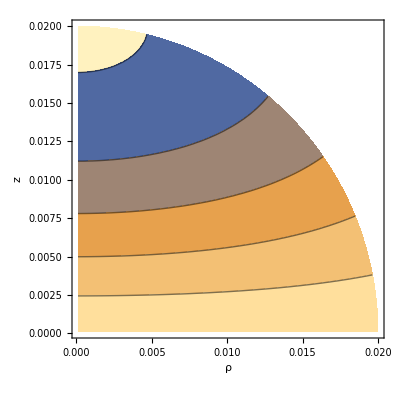
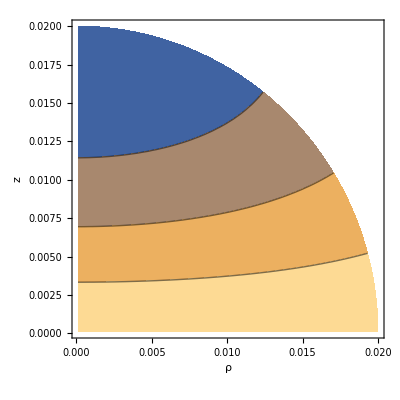
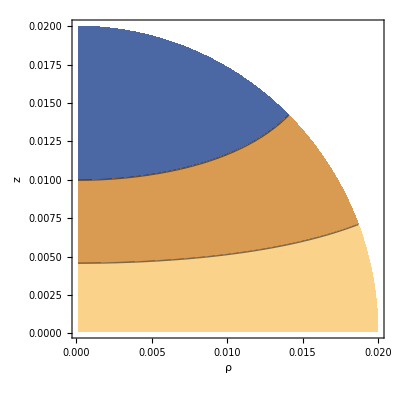
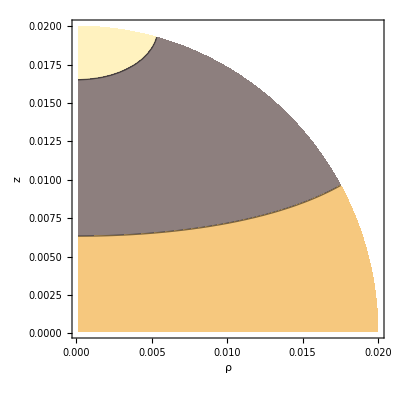

```mathematica
Table[ContourPlot[T[Sqrt[ρ^2 + z^2],ArcTan[ρ/z],t] ,{ρ,0.0001,a},{z,0.0001,a},Contours->Table[300+10 n,{n,0,10}],FrameLabel->{"ρ","z"},RegionFunction->Function[{ρ,z},ρ^2 + z^2≤ a^2]],{t,0,2000,200}]
```

5.1.3

(3) Water waves in water of depth h have a dispersion relation given by the equation ω =√(g k tanh k h), where  g is the acceleration of gravity, g = 9.8 m/s^2. [See Kundu (1990, pg.194).] Plot the phase and group velocities of these waves, in meters per second, as a function of k h. Show analytically that in the limit that k h>>1  (deep water waves) the phase velocity is twice the group velocity.

### Solution

```mathematica
Clear["Global`*"]
```

```mathematica
ω[k_] = Sqrt[g k Tanh[k h]];
```

```mathematica
vϕ[k_] = ω[k]/k
```

(√(g k Tanh[h k]))/k

```mathematica
vg[k_] = ω'[k]//FullSimplify
```

(g (h k Sech[h k]^2+Tanh[h k]))/(2 √(g k Tanh[h k]))

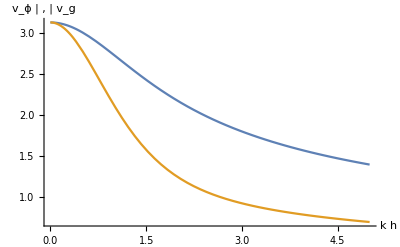

```mathematica
Plot[{vϕ[k],vg[k]}/.{g->9.8,h->1}//Evaluate,{k,0,5},AxesLabel->{"k h",Grid[{{Style["v_ϕ",Blue],",",Style["v_g",Purple]}},Spacings->0.2]}]
```

```mathematica
Series[vg[k]/vϕ[k],{k,Infinity,0}]//Normal//Simplify
```

1/2+h k Csch[2 h k]

Since Csch[x]→ 0 as x→ ∞, the ratio of group to phase velocities approaches 1/2 as k h→ ∞.

5.1.5(b)

(5) Find the solution to the heat equation with χ=1 for the following initial conditions

(b) T(x,0) = h(x), where h(x)is a Heaviside step function.  Animate the solution on -5<x<5 for 0<t<2.

### Solution

The general solution for the temperature evolution is 
T(x,t) = ∫ⅆk/(2π)ⅇ^(ⅈ k x-χ k^2 t) (T̃)_o(k).

All we need do is find (T̃)_o(k) and perform the required inverse Fourier transform. Since T_o(x) = h(x),

```mathematica
Clear["Global`*"]
```

```mathematica
T̃[k_] =Simplify[Expand[FourierTransform[UnitStep[x],x,-k] Sqrt[2Pi]]]
```

-ⅈ/k+π DiracDelta[k]

Then

```mathematica
T[x_,t_] =Simplify[InverseFourierTransform[ T̃[k] Exp[-k^2 t],k,-x]/Sqrt[2Pi]]
```

1/2 (1+Erf[x/(2 √t)])

```mathematica
Table[Plot[T[x,t],{x,-5,5},PlotRange->{{-5,5},{0,1}}],{t,0.0001,2,.1}];
```

```mathematica
ListAnimate[%]
```

5.1.16

(16) In an exploding-wire experiment, a long thin wire is subjected to an extremely large current, causing the wire to vaporize and explode. (Such explosions are used as x-ray sources, and to study the properties of hot dense materials.) Assuming that the wire creates a pressure source of the form S(r,t)=s h(t) δ(x)δ(y) where  h(t) is a Heaviside function, solve Eq. (5.1.79) for the resulting pressure wave, assuming that p=0 for t<0. Show that

p(r,t) ={s/(2π  c^2)log[c t/r+√(c^2 t^2/r^2-1)],      r≤ c t,
0,                                                                           r> c t,

where  r is the cylindrical radial coordinate. Taking c=s=1, animate p(r,t) for 0<t<10.  
[Hint: Find the solution for p in terms of an inverse Fourier transform involving k=(k_x,k_y). Then write k·(x,y)=k r cos θ, where θ is the angle between k and r=(x,y),  and perform the integral over k in polar coordinates (k,θ) where k_x = k cos θ, k_y= k sin θ. In these coordinates, ⅆ^2 k=k ⅆk ⅆθ. ]

### Solution

```mathematica
Clear["Global`*"]
```

We are to solve

∂^2/(∂t^2)p(r,t)= c^2∇^2 p(r,t) +s h(t) δ(x)δ(y).

Fourier transforming in space  and time we obtain

p(r,t)=∫(ⅆωⅆ^2 k)/(2 π)^3(S̃(k,ω))/(c^2 k^2-ω^2)ⅇ^(ⅈ( k·r-ω t)).

Where S̃(k,ω)is the transform of the source. The Fourier transform of the delta functions gives one, and of a step function yields

```mathematica
stilde[k_,ω_] =s Expand[FourierTransform[UnitStep[t],t,ω] Sqrt[2 Pi]]
```

s (ⅈ/ω+π DiracDelta[ω])

Performing the inverse time-transform yields

```mathematica
ptilde[k_,t_] = InverseFourierTransform[stilde[k,ω]/(c^2 k^2 -ω^2),ω,t]/Sqrt[2Pi]
```

1/(4 c^2 k^2)ⅇ^(-ⅈ c k t) s (Sign[t] (-(-1+ⅇ^(ⅈ c k t))^2+(1+ⅇ^(2 ⅈ c k t)) Sign[Abs[Im[c k]]])+2 (ⅇ^(ⅈ c k t)+HeavisideTheta[-t Sign[Im[c k]]] Sign[Im[c k]]-ⅇ^(2 ⅈ c k t) HeavisideTheta[t Sign[Im[c k]]] Sign[Im[c k]]))

```mathematica
Simplify[%,c>0&&k>0]
```

(s (2-ⅇ^(-ⅈ c k t) (-1+ⅇ^(ⅈ c k t))^2 Sign[t]))/(4 c^2 k^2)

```mathematica
Simplify[%,t<0]
```

(ⅇ^(-ⅈ c k t) (1+ⅇ^(2 ⅈ c k t)) s)/(4 c^2 k^2)

This solution is nonzero for t<0 so add in a homogeneous solution ,

```mathematica
ptilde[k_,t_] = Simplify[%%-% ]
```

-(ⅇ^(-ⅈ c k t) (-1+ⅇ^(ⅈ c k t))^2 s (1+Sign[t]))/(4 c^2 k^2)

we only care about this for t>0:

```mathematica
ptilde[k_,t_] = FullSimplify[ptilde[k,t],t>0]
```

(s-s Cos[c k t])/(c^2 k^2)

We could also have obtained this result using the green’s function  for the harmonic oscillator.

Now we must inverse transform this in space. Use cylindrical coordinates to write ⅇ^(ⅈ( k·r))= ⅇ^(ⅈ k r cosθ). Then 
∫(ⅆ^2 k)/(2 π)^2 ⅇ^(ⅈ k r cosθ)p̃(k,t)=∫kⅆkⅆθ/(2 π)^2 ⅇ^(ⅈ k r cosθ)p̃(k,t)=∫kⅆk/(2 π)^2 2π J_o(k r)p̃(k,t). Now for the final integral:

```mathematica
p[r_,t_] = Integrate[% BesselJ[0,k r] k,{k,0,Infinity},Assumptions-> 0<r<c t && c>0 &&t>0]/(2 Pi)
```

(s Log[(c t+√(-r^2+c^2 t^2))/r])/(2 c^2 π)

This is the correct solution in the range c t > r. For c t <r, the solution is zero because waves have not had a chance to propagate there yet:

```mathematica
Integrate[ptilde[k,t] BesselJ[0,k r] k,{k,0,Infinity},Assumptions-> 0<c t<r && c>0 &&t>0]/(2 Pi)
```

0

```mathematica
p[r_,t_] = UnitStep[t] p[r,t]UnitStep[c t-r]
```

(s Log[(c t+√(-r^2+c^2 t^2))/r] UnitStep[t] UnitStep[-r+c t])/(2 c^2 π)

```mathematica
c=1;s=1;
```

```mathematica
Table[Plot[p[r,t],{r,0,2},PlotRange->{0,1.5}],{t,0,2,.1}];
ListAnimate[%]
```

5.1.28

(28) Whistler waves are low-frequency electromagnetic waves that propagate along the magnetic field in a magnetized plasma. They have the following dispersion relation:

ω = Ω_c c^2 k^2/ω_p^2,

where Ω_c=e B/m is the electron cyclotron frequency, we have assumed that k  is parallel to the magnetic field, and we have also assumed that  c k << ω<<Ω_c. [See  Stix (1962, pg. 55).]

(a) A group of whistler waves is created by a lightning flash in the upper atmosphere. The waves propagate  along the earth's magnetic field in the ionospheric plasma, according to E(x,t) =2 Re∫ⅆk/(2π)A(k) ⅇ^(ⅈ (k x-ω(k) t)), where x is the distance along the magnetic field. Taking A(k) = ⅇ^(-k^2/k_o^2), find the evolution of the wave packet analytically, without approximation. Animate the evolution for the following parameters: k_o = 0.01 m^-1, Ω_c= 10^5 s^-1, and ω_p= 10^7 s^-1, and for 0<t<0.01  s.

(b) A radio receiver is 3000 kilometers away from the initial location of the lightning flash, as measured along the magnetic field. Using the Play function, play the sound that the whistler waves make as they are picked up by the receiver. (A good time range is from zero to 5 seconds).  Explain qualitatively why you hear a descending tone (this is why they are called whistler waves!). (Hint: how does the phase velocity depend on frequency?) To hear the sound of real whistler waves, picked up by the University of Iowa's plasma wave instrument on NASA's POLAR spacecraft, go to the following link: http://www-pw.physics.uiowa.edu/plasma-wave/istp/polar/magnetosound.html

(c) For propagation that is not aligned with the magnetic field, the whistler wave dispersion relation is 
ω = Ω_c c^2 k^2 cos θ/ω_p^2, where θ is the angle between k and the magnetic field. Show that this dispersion relation implies that the angle  between the group velocity and the magnetic field is always less than 19.5 °. Hence, the earth's magnetic field guides these waves.

### Solution

#### (a)

```mathematica
Clear["Global`*"]
```

```mathematica
ω[k_] = Ωc c^2 k^2/ωp^2;
```

```mathematica
A[k_] = Exp[-k^2/k0^2];
```

```mathematica
Ef[x_,t_] = 2 Re[ Integrate[A[k] Exp[I k x - I ω[k] t],{k,-Infinity,Infinity}, Assumptions->Im[x]==0&&Im[(c^2 t Ωc)/ωp^2]<Re[1/k0^2]]/(2 Pi)]
```

Re[(ⅇ^(-x^2/(4 (1/k0^2+(ⅈ c^2 t Ωc)/ωp^2))))/(√(1/k0^2+(ⅈ c^2 t Ωc)/ωp^2))]/(√π)

```mathematica
c=3 10^8; k0 = 0.01; Ωc = 10^5; ωp = 10^7;
```

```mathematica
Table[Plot[Ef[x,t],{x,-10000,10000},PlotRange->{-.003,.006}],{t,0,.01,.0005}];
```

```mathematica
ListAnimate[%]
```

#### (b)

```mathematica
Play[Ef[3000 10^3,t],{t,0,5}]
```

-Graphics-

The descending tone occurs because high frequencies propagate faster than lower frequencies, reaching the receiver first.

#### (c)

Since ω = Ω_c c^2 k^2 cos θ/ω_p^2=Ω_c c^2 k  k_z/ω_p^2, write k=√(k_x^2+k_y^2+k_z^2). Then v_g=Ω_c c^2/ω_p^2 (k_z k_x/k, k_z k_y/k, k + k_z^2/k) . The angle α this vector makes with the magnetic field is given by cos α = v_gz/|v_g| =(k + k_z^2/k)/√(k_z^2( k_x^2+  k_y^2)/k^2+(k + k_z^2/k)^2). Simplify this expression, using k_x^2+  k_y^2≡k^2 sin^2 θ, and  k_z = k cos θ where θis the angle the wavevector makes with the magnetic field (as opposed to α. the angle the group velocity has with the magnetic field)..

```mathematica
FullSimplify[(k + Subscript[k, z]^2/k)/√(Subscript[k, z]^2( Subscript[k, x]^2+  Subscript[k, y]^2)/k^2+(k + Subscript[k, z]^2/k)^2)/.{Subscript[k, x]^2+  Subscript[k, y]^2-> k^2 Sin[θ]^2, Subscript[k, z]-> k Cos[θ]},k>0]
```

(3+Cos[2 θ])/(√(10+6 Cos[2 θ]))

```mathematica
α[θ_] = ArcCos[%]
```

ArcCos[(3+Cos[2 θ])/(√(10+6 Cos[2 θ]))]

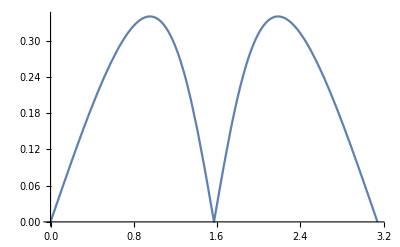

```mathematica
Plot[α[θ],{θ,0,Pi}]
```

α  takes on a maximum possible value. Determine it :

```mathematica
D[α[θ],θ]
```

-((6 (3+Cos[2 θ]) Sin[2 θ])/(10+6 Cos[2 θ])^(3/2)-(2 Sin[2 θ])/(√(10+6 Cos[2 θ])))/(√(1-(3+Cos[2 θ])^2/(10+6 Cos[2 θ])))

```mathematica
Solve[Numerator[%]==0,θ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→0},{θ→-π/2},{θ→π/2},{θ→-ArcCos[-1/(√3)]},{θ→ArcCos[-1/(√3)]},{θ→-ArcCos[1/(√3)]},{θ→ArcCos[1/(√3)]}}

Maximum angle is at θ=  ArcCos[-1/Sqrt(3)] so α_max is, in degrees,

```mathematica
α[ ArcCos[-1/Sqrt[3]]]//FullSimplify
```

ArcCos[(2 √2)/3]

```mathematica
%/Degree//N
```

19.4712